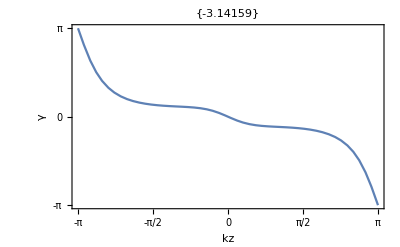
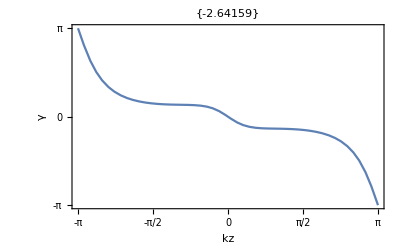
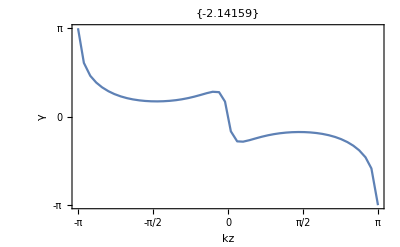
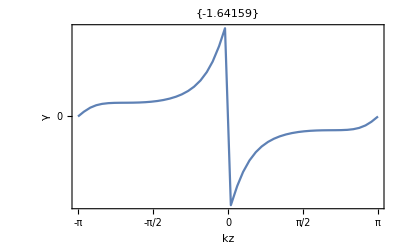
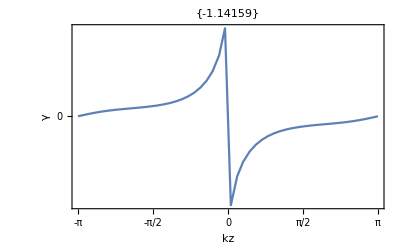
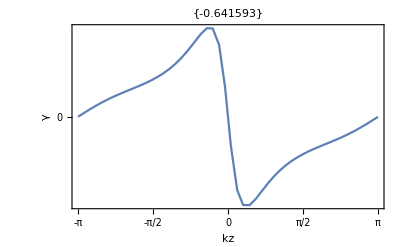
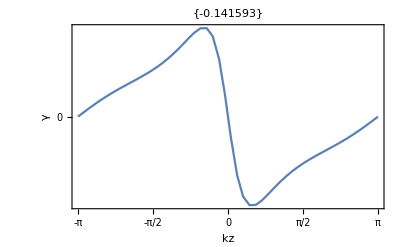
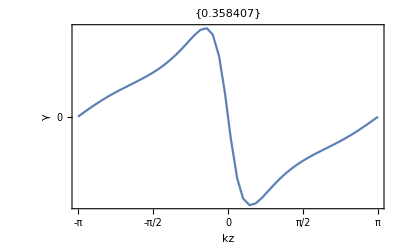

output.pdf

```mathematica
ClearAll["Global`*"]
k0=1;
t=1;(*hopping amplitude*)
m=1;(*mass amplitude*)
numOfstep=30;(*number of iterating steps*)
H[kx_,ky_,kz_,t_,m_,k0_]:=(m(2-Cos[ky]-Cos[kz])+2t(Cos[kx]-Cos[k0]))PauliMatrix[1]+2 t Sin[ky]PauliMatrix[2]+2t Sin[kz]PauliMatrix[3]//N(*Hamiltonian*)


posi[kx_,ky_,kz_]:=Sign[Eigensystem[
H[kx,ky,kz,t,m,k0]][[1]].{-1,1}];

eigenvec[kx_,ky_,kz_]:=
{Normalize[Transpose[
Eigensystem[
H[kx,ky,kz,t,m,k0]]//Transpose][[2,posi[kx,ky,kz]]]]}//Transpose

coupMatrix[kxx_,kyy_,kzz_]:=Dot[eigenvec[kxx,kyy,kzz],eigenvec[kxx,kyy,kzz]//ConjugateTranspose];(*coupling matrix*)

a= Table[Plot[
vecInitial=eigenvec[kx,-Pi,kz];
-Arg@Dot[vecInitial//ConjugateTranspose,
Dot@@
Table[coupMatrix[kx,ky,kz],{ky,-Pi,Pi,2Pi/numOfstep}](*prod of coupling mat (ky=-Π -> ky=Π)*)
,vecInitial][[1,1]],{kz,-Pi,Pi},PlotPoints->50,MaxRecursion->0,Frame->True,FrameLabel->{"kz","γ"},FrameTicks->{{-Pi,-Pi/2,0,Pi/2,Pi},{-Pi,0,Pi}},PlotLabel->{N@kx}],{kx,-Pi,Pi,0.5}];
a
Export["output.pdf",a]
```

```mathematica
SystemOpen["output.pdf"]
```